```mathematica
hedge=Flatten[Import["c:\\book1.txt","Table"],1];
```

```mathematica
Length[hedge]
```

892

```mathematica
g=FinancialData["DAX","1.1.2000"];
```

```mathematica
dax=Transpose[g][[2]][[1;;Length[hedge]]];
```

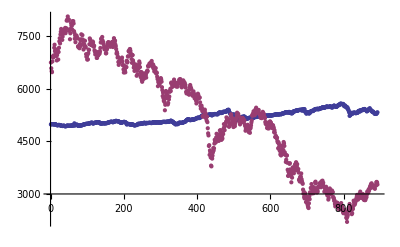

```mathematica
ListPlot[{hedge,dax}]
```

```mathematica
hedge=Log[hedge];dax=Log[dax];
```

```mathematica
hedge=Differences[hedge];
```

```mathematica
dax=Differences[dax];
```

```mathematica
w=Transpose[{hedge,dax}];
```

```mathematica
w=Sort[w,#1[[1]]<#2[[1]]&];
```

```mathematica
hedge=Transpose[w][[1]];
dax=Transpose[w][[2]];
```

```mathematica
w[[2]]
```

{-0.0117745,0.0306036}

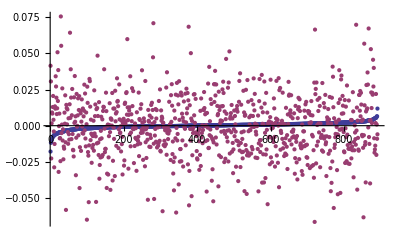

```mathematica
ListPlot[Transpose[w],PlotRange->All]
```

```mathematica
nN=20;wN=Length[hedge];
m0=Min[Transpose[w][[1]]]
Max[Transpose[w][[1]]]
m1=Min[Transpose[w][[2]]]
Max[Transpose[w][[2]]]
f0=(nN-1)/(Max[Transpose[w][[1]]]-m0)
f1=(nN-1)/(Max[Transpose[w][[2]]]-m1)
d=1/wN//N
```

-0.0178719

0.0118256

-0.0665223

0.0755268

639.785

133.757

0.00112233

```mathematica
F={};For[i=1,i≤wN,i++,
For[j=1,j≤wN,j++,
m=0;
If[w[[j,1]]<=w[[i,1]]  && w[[j,2]]≤w[[i,2]],m++;];
];
AppendTo[F,{w[[i,1]],w[[i,2]],m/wN}];
]
```

$Aborted

```mathematica
U={};nN=20;For[i=0,i≤nN,i++,
AppendTo[U,{min0,i/nN*(max1-min1)+min1,0}];
]
For[i=0,i≤nN,i++,
AppendTo[U,{i/nN*(max0-min0)+min0,min1,0}];
]
For[i=0,i≤nN,i++,
AppendTo[U,{max0,i/nN*(max1-min1)+min1,Length[Select[w,#[[1]]<=max0  && #[[2]]<=i/nN*(max1-min1)+min1&]]/wN}];
]
For[i=0,i≤nN,i++,
AppendTo[U,{i/nN*(max0-min0)+min0,max1,Length[Select[w,#[[2]]<=max1  && #[[1]]<=i/nN*(max0-min0)+min0&]]/wN}];
]
```

```mathematica
min0=Min[Transpose[w][[1]]];
max0=Max[Transpose[w][[1]]];
min1=Min[Transpose[w][[2]]];
max1=Max[Transpose[w][[2]]];
```

```mathematica
U={};sdax=Sort[dax];AppendTo[U,{max0,max1,1}];

For[i=1,i≤nn,i++,
AppendTo[U,{hedge[[i]],max1,(i-1)/nn}];
AppendTo[U,{max0,sdax[[i]],(i-1)/nn}];
AppendTo[U,{hedge[[i]],min1,0}];
]
```

```mathematica
F={};For[i=1,i≤wN,i++,
AppendTo[F,{w[[i,1]],w[[i,2]],Length[Select[w,#[[1]]<w[[i,1]]  && #[[2]]<w[[i,2]]&]]/wN}];
]
```

```mathematica
W=Join[F,U];
```

```mathematica
ListPointPlot3D[W]
```

-Graphics3D-

```mathematica
ww={};
For[i=1,i≤nn,i++,
AppendTo[ww,Select[W,#[[1]]==hedge[[i]]&]];
]
```

```mathematica
Length[W]
Length[Flatten[ww,1]]
```

2675

2759

```mathematica
W[[1]]
```

{-0.0178719,0.041439,0}

```mathematica
ww[[9]]
```

{{-0.00741427,0.00408647,2/891},{-0.00741427,0.0755268,8/891}}

```mathematica
ListPointPlot3D[Flatten[ww,1]]
```

-Graphics3D-

```mathematica
Select[W,#[[1]]==hedge[[3]]&]
```

{{-0.0114726,-0.0226471,0},{-0.0114726,0.0755268,2/891}}

```mathematica
ListPointPlot3D[Select[W,#[[1]]==hedge[[3]]&]]
```

-Graphics3D-

```mathematica
w[[2]]
```

```mathematica
Length[Flatten[w,1]]
```

891

```mathematica
Length[W]
```

4455

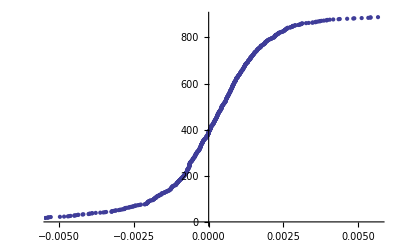

```mathematica
ListPlot[hrand]
```

```mathematica
nn=Length[hedge]
```

891

```mathematica
f=Interpolation[Join[F,U]]
```

Interpolation::indim: The coordinates do not lie on a structured tensor product grid.

```mathematica
F[[1,1]]
```

{-0.0665223,-0.0178719,0}

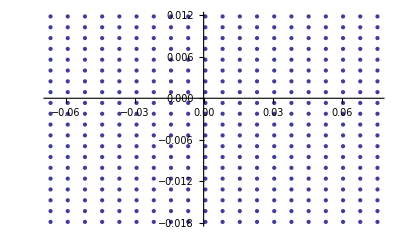

```mathematica
ListPlot[Transpose[Transpose[Q][[1;;2]]]]
```

```mathematica
w[[1]]
```

{0.041439,-0.0178719}

```mathematica
F=Table[{m0+i/f0,m1+j/f1,0},{i,0,nN-1},{j,0,nN-1}];For[i=1,i≤nN,i++,
For[j=1,j≤nN,j++,
For[k=1,k≤wN,k++,
If[w[[k,2]]≤F[[i,j,2]] &&w[[k,1]]≤F[[i,j,1]] ,F[[i,j,3]]+=d;];
]
]];Q=Flatten[F,1];
```

```mathematica
ListPointPlot3D[Q]
```

-Graphics3D-

```mathematica
w=Import["c:\\Trivariat.txt","Table"];
```

```mathematica
Length[w]
```

8000

```mathematica
w[[8000]]
```

{0.011826,0.075527,0.011826,1.}

```mathematica
w1=Select[w,#[[1]]==w[[5000,1]]&];
```

```mathematica
fif=Transpose[Transpose[w1][[2;;4]]];
```

```mathematica
ListPointPlot3D[fif]
```

-Graphics3D-

```mathematica
w[[3]]
```

{-0.017872,-0.063653,0.}

```mathematica
Length[w]
```

10000

```mathematica
w[[1000,2]]
```

0.075527

```mathematica
Table[p,{p,1,9999,1000}]
```

{1,1001,2001,3001,4001,5001,6001,7001,8001,9001}

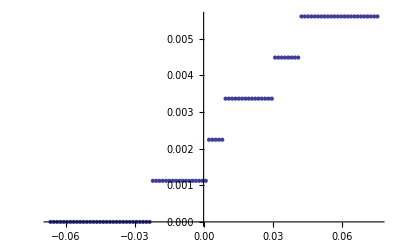

```mathematica
p=3000;ListPlot[{#[[2]],#[[3]]}&/@Select[w,#[[1]]==w[[p,1]]&]]
```

```mathematica
ll={#[[2]],#[[3]]}&/@Select[w,#[[1]]==w[[p,1]]&];
```

```mathematica
ListPlot[ll]
```

-Graphics-

```mathematica
Max[Table[w[[k,3]]-Q[[k,3]],{k,nN^2}]]
```

4.74747×10^-7